```mathematica
ComplexExpand[1/(x+I y)]
```

x/(x^2+y^2)-(ⅈ y)/(x^2+y^2)

```mathematica
u = x/(x^2+y^2); v=-y/(x^2 + y^2);
```

```mathematica
r[η_,ξ_]={x,y}/.Solve[{u==η,v==ξ},{x,y}] [[1]]
```

{η/(η^2+ξ^2),-ξ/(η^2+ξ^2)}

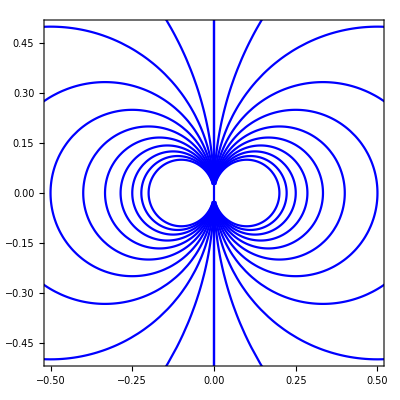

```mathematica
xiPlot=ParametricPlot[Table[r[η,ξ],{η,-5,5,1/2}],{ξ,-40,40},PlotRange->{{-1/2,1/2},{-1/2,1/2}},PlotStyle->Blue]
```

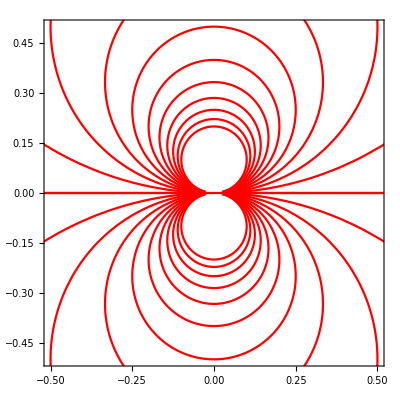

```mathematica
etaPlot=ParametricPlot[Table[r[η,ξ],{ξ,-5,5,1/2}],{η,-40,40},PlotRange->{{-1/2,1/2},{-1/2,1/2}},PlotStyle->Red]
```

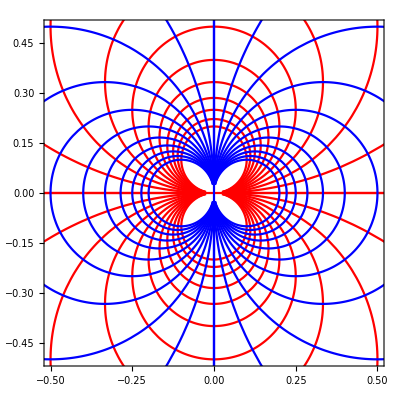

```mathematica
Show[etaPlot,xiPlot,PlotRange->{{-1/2,1/2},{-1/2,1/2}}]
```

```mathematica
DrDη=D[r[η,ξ],η]//FullSimplify
```

{(ξ^2-η^2)/((η^2+ξ^2)^2),(2 η ξ)/((η^2+ξ^2)^2)}

```mathematica
Subscript[h, η]=Norm[DrDη]//ComplexExpand//FullSimplify//PowerExpand
```

1/(η^2+ξ^2)

```mathematica
DrDξ=D[r[η,ξ],ξ]//FullSimplify
```

{-(2 η ξ)/((η^2+ξ^2)^2),(ξ^2-η^2)/((η^2+ξ^2)^2)}

```mathematica
Subscript[h, ξ]=Norm[DrDξ]//ComplexExpand//FullSimplify//PowerExpand
```

1/(η^2+ξ^2)

```mathematica
Subscript[e, η]=DrDη/Subscript[h, η]
```

{(ξ^2-η^2)/(η^2+ξ^2),(2 η ξ)/(η^2+ξ^2)}

```mathematica
Subscript[e, ξ]=DrDξ/Subscript[h, ξ]
```

{-(2 η ξ)/(η^2+ξ^2),(ξ^2-η^2)/(η^2+ξ^2)}